## Part 1 - Defining the Variables

First, we start off the defining the gravitational constant, G, the masses of the star, planet, and moon, and their respective distance from their orbital parents. We’ll use SI units for now but also set G=100 for simplicity. Later on, however, we’ll use a more realistic gravitational constant. The masses of the star, planet, and moon, respectively, are m1, m2, and m3 and their respective orbital distances from their orbital parents are r1, r2, and r3 (the star’s orbital distance is 0 because it’s the most massive body in the system).

```mathematica
G=100

m1=50
m2=0.0001
m3=0.000002

r1i={0,0}
r2i={50,0}
r3i={0.1,0}
```

100

50

0.0001

2.×10^-6

{0,0}

{50,0}

{0.1,0}

## Part 2 - Defining the Functions and Diff. Equations

Now let’s define the differential equations based on both Newtonian mechanics and Kepler’s laws of planetary motion.

```mathematica
r1[t_]:={x1[t],y1[t]}
r2[t_]:={x2[t],y2[t]}
r3[t_]:={x3[t],y3[t]}

r12[t_]:=r2[t]-r1[t]
r13[t_]:=r3[t]-r1[t]

r21[t_]:=r1[t]-r2[t]
r23[t_]:=r3[t]-r2[t]

r31[t_]:=r1[t]-r3[t]
r32[t_]:=r2[t]-r3[t]

acc1[t_]:={G*m2*Normalize[r12[t]][[1]]/(Norm[r12[t]])^2,G*m2*Normalize[r12[t]][[2]]/(Norm[r12[t]])^2}+{G*m3*Normalize[r13[t]][[1]]/(Norm[r13[t]])^2,G*m3*Normalize[r13[t]][[2]]/(Norm[r13[t]])^2}
acc2[t_]:={G*m1*Normalize[r21[t]][[1]]/(Norm[r21[t]])^2,G*m1*Normalize[r21[t]][[2]]/(Norm[r21[t]])^2}+{G*m3*Normalize[r23[t]][[1]]/(Norm[r23[t]])^2,G*m3*Normalize[r23[t]][[2]]/(Norm[r23[t]])^2}
acc3[t_]:={G*m1*Normalize[r31[t]][[1]]/(Norm[r31[t]])^2,G*m1*Normalize[r31[t]][[2]]/(Norm[r31[t]])^2}+{G*m2*Normalize[r32[t]][[1]]/(Norm[r32[t]])^2,G*m2*Normalize[r32[t]][[2]]/(Norm[r32[t]])^2}
```

## Part 3 - Setting Up the Initial Acc. and Velocities

We’ll use the concepts of tangential velocity and centripetal acceleration to find the initial velocities needed to keep them in circular orbits and the initial accelerations that make them go in orbit in the first place. The acceleration functions defined above represent the second time derivatives of the position functions of each celestial body.

```mathematica
acc1i={0,0};
acc2i={G*m1*Normalize[r2i][[1]]/Norm[r2i]^2,G*m1*Normalize[r2i][[2]]/Norm[r2i]^2};
acc3i={G*m2*Normalize[r3i][[1]]/Norm[r3i]^2,G*m2*Normalize[r3i][[2]]/Norm[r3i]^2};

v1i={0,0};
v2i={0,Sqrt[Norm[r2i]*Norm[acc2i]]};
v3i={0,-Sqrt[Norm[r3i]*Norm[acc3i]]}+v2i;

v1i//MatrixForm
v2i//MatrixForm
v3i//MatrixForm
```

(0
0)

(0
10)

(0
9.68377)

## Part 4 - Solving the Differential Equation

Now we’ll set the initial conditions and get ready to solve these differential equations.

```mathematica
solution=NDSolve[{x1''[t]==acc1[t][[1]],y1''[t]==acc1[t][[2]],x2''[t]==acc2[t][[1]],y2''[t]==acc2[t][[2]],x3''[t]==acc3[t][[1]],y3''[t]==acc3[t][[2]],x1[0]==r1i[[1]],y1[0]==r1i[[2]],x2[0]==r2i[[1]],y2[0]==r2i[[2]],x3[0]==r2i[[1]]+r3i[[1]],y3[0]==r2i[[2]]+r3i[[2]],x1'[0]==v1i[[1]],y1'[0]==v1i[[2]],x2'[0]==v2i[[1]],y2'[0]==v2i[[2]],x3'[0]==v3i[[1]],y3'[0]==v3i[[2]]},{x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]},{t,0,100}];

x1sol=x1[t]/.solution[[1]];
y1sol=y1[t]/.solution[[1]];

x2sol=x2[t]/.solution[[1]];
y2sol=y2[t]/.solution[[1]];

x3sol=x3[t]/.solution[[1]];
y3sol=y3[t]/.solution[[1]];
```

## Part 5 - Graphing the Results

Now we’re going to graph the motions of each object relative to the origin (you can see that the star moves a little bit but not nearly as much as the other celestial bodies).

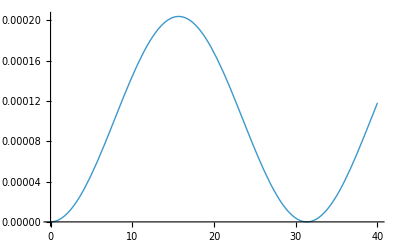

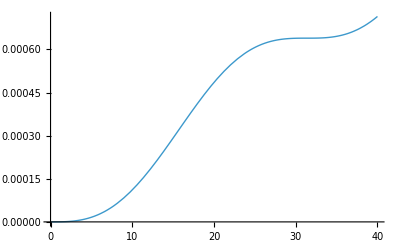

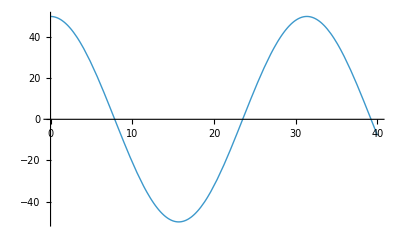

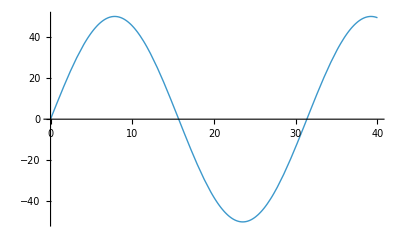

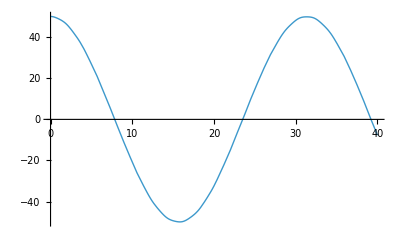

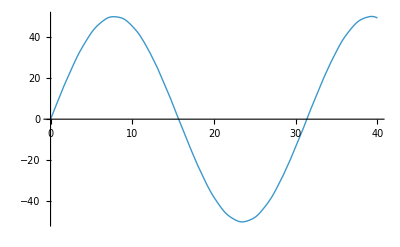

```mathematica
Plot[x1sol,{t,0,40},PlotStyle->Thick,PlotRange->All]
Plot[y1sol,{t,0,40},PlotStyle->Thick,PlotRange->All]

Plot[x2sol,{t,0,40},PlotStyle->Thick,PlotRange->All]
Plot[y2sol,{t,0,40},PlotStyle->Thick,PlotRange->All]

Plot[x3sol,{t,0,40},PlotStyle->Thick,PlotRange->All]
Plot[y3sol,{t,0,40},PlotStyle->Thick,PlotRange->All]
```

Now we can subtract the motion of the planet around the original from the motion of the moon around the origin to get the motion of the moon around the planet.

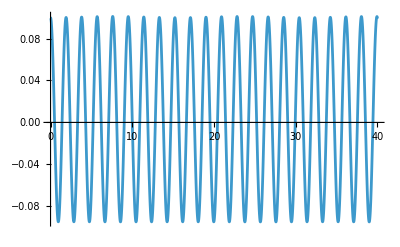

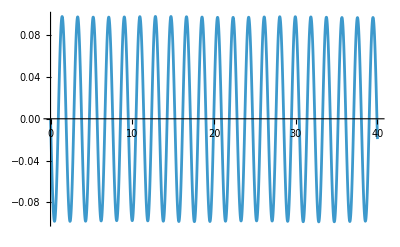

```mathematica
Plot[x3sol-x2sol,{t,0,40},PlotRange->All]
Plot[y3sol-y2sol,{t,0,40},PlotRange->All]
```

Because they moon’s orbit is so much faster than the planet, let’s limit the time range a bit on these graphs to get a better look at the moon’s orbit.

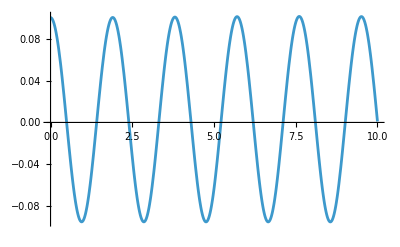

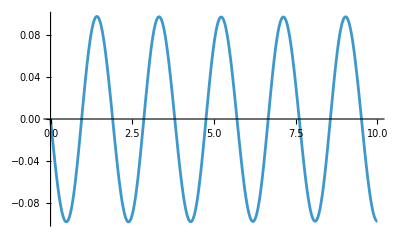

```mathematica
Plot[x3sol-x2sol,{t,0,10},PlotRange->All]
Plot[y3sol-y2sol,{t,0,10},PlotRange->All]
```

## Part 6 - Double-Checking the Results

Let’s use Newton’s version of Kepler’s 3rd law of planetary motion to predict the orbital periods of the planet and the moon around the star as T1 and T2, respectively. The star doesn’t move very much and its distance from the origin is always negligible as we saw in the graph of its motion. This formula describing the orbital motion of celestial bodies is shown down below:

-Graphics-

```mathematica
T2=Sqrt[4*Pi^2*(Norm[r2i])^3/(G*(m1+m2))]
T3=Sqrt[4*Pi^2*(Norm[r3i])^3/(G*(m2+m3))]
```

31.4159

1.96734

Now we can test these by making certain trig-derived functions based on these orbital periods and comparing them to the actual motions of the planet and moon. Let’s start off with the orbital motion of the planet around the star.

0.031831

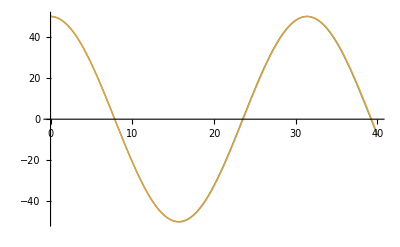

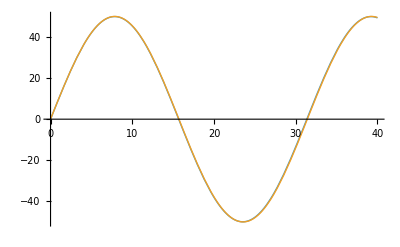

```mathematica
f2=1/T2

Plot[{x2sol,50Cos[2*Pi*f2*t]},{t,0,40},PlotStyle->Thick,PlotRange->All]
Plot[{y2sol,50Sin[2*Pi*f2*t]},{t,0,40},PlotStyle->Thick,PlotRange->All]
```

Alright, it looks pretty  close. There’s just a slight computational error. Now let’s do the moon’s orbital motion. The moon’s orbital motion around the planet starts off with a negative y-velocity relative to the planet, so we’ll have to add a negative sine wave for the y-component of the moon’s orbital path.

0.5083

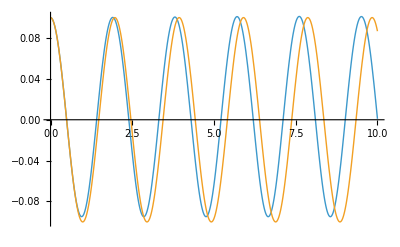

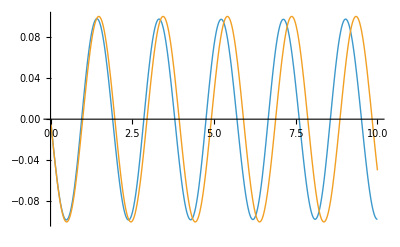

```mathematica
f3=1/T3

Plot[{x3sol-x2sol,0.1Cos[2*Pi*f3*t]},{t,0,10},PlotStyle->Thick,PlotRange->All]
Plot[{y3sol-y2sol,-0.1Sin[2*Pi*f3*t]},{t,0,10},PlotStyle->Thick,PlotRange->All]
```

The computational error of the moon’s orbital period seems to be greater than that of the planet’s orbital period. But either way, these equations do seem pretty useful for predicting the motions of moons in orbit around planets which are, in turn, in orbit around stars.

## Part 7 - Resulting Equation

Here are the equations of the planet’s x- and y-coordinates (with the star at the center of the orbit):

```mathematica
x2[t_]=50*Cos[2*Pi*f2*t]
y2[t_]=50*Sin[2*Pi*f2*t]
```

50 Cos[0.2 t]

50 Sin[0.2 t]

Here are the equations describing the moon’s x- and y-coordinates (with the planet at the center of the orbit):

```mathematica
x3[t_]=0.1*Cos[2*Pi*f3*t]
y3[t_]=-0.1*Sin[2*Pi*f3*t]
```

0.1 Cos[3.19374 t]

-0.1 Sin[3.19374 t]

We  can also define these equations to be relative to the star’s position:

```mathematica
x23[t_]=x2[t]+x3[t]
y23[t_]=y2[t]+y3[t]
```

50 Cos[0.2 t]+0.1 Cos[3.19374 t]

50 Sin[0.2 t]-0.1 Sin[3.19374 t]

Let’s define the following variables: ‘a’ is the semi-major axis of the orbit which we’ll assume is the radius of a perfectly circular orbit, ‘G’ is the gravitational constant, ‘M’ is the mass of the larger body, ‘m’ is the mass of the smaller body. Now for the general equations of the coordinates of a body in orbit around another body with significantly more mass. Let’s assume that the smaller body’s position starts with a positive x-coordinate and no y-coordinate so we can simplify the functions into cosine and sine. Here are the general formulae:

```mathematica
T=Sqrt[4*Pi^2*a^3/(G*(M+m))]
f=1/T

x[t_]=a*Cos[2*Pi*f*t]
y[t_]=a*Sin[2*Pi*f*t]
```

1/5 √(a^3/(m+M)) π

5/(√(a^3/(m+M)) π)

a Cos[(10 t)/(√(a^3/(m+M)))]

a Sin[(10 t)/(√(a^3/(m+M)))]